Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

5 - 8 Electrostatic Potential. Steady-State Heat Problems.

The electrostatic potential satisfies Laplace's equation ∇^2 in any region free of charges. Also the heat equation u_t=c^2∇^2 u  (Sec. 12.5) reduces to Laplace's equation if the temperature u is time independent ("steady-state case"). Using numbered line (20), p. 591, find the potential (equivalently: the steady-state temperature) in the disk r<1 if the boundary values are (sketch them, to see what is going on).

5. u(1,θ)=220 if    -1/2π<θ<1/2 π and 0 otherwise

```mathematica
Clear["Global`*"]
```

Looking at some polar coordinate solutions of wave equation problems, I see that the usual basic approach is to consider the function f(r), then get the section form of the deflection shape on a radius and calculate u from there, by revolving. However, in this problem the text prefers to consider the function f(θ), which is needed only in the case of a deflection shape which is not radially symmetric (for example, see https://www.math.uni-sb.de/ag/fuchs/PDE14-15/pde14-15-lecture-16.pdf). (For a complete example using f(r), see the bottom of this notebook, under the heading “Extra Inserted Material.”) Since the current problem is covered in the s.m. I just follow that. I need numbered line (20) from p. 591.

u[r,θ]=a_0+Sum[a_n(r/R)^n Cos[n θ]+b_n(r/R)^n Sin[n θ],{n,1,∞}]

```mathematica
u[1,θ_]=f[θ_]=Piecewise[{{220,-π/2<θ<π/2}}]
```

Piecewise[{{220, -π/2<θ<π/2}, {0, True}}]

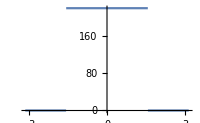

```mathematica
Plot[f[θ],{θ,-π,π},ImageSize->200]
```

I observe that f(θ) is an even function. Also the problem description tells me to use (20), which is a periodic function. The s.m. deduces somehow that the period of f(θ) is 2π. I am advised to use numbered line (6*) from p. 486:

a_0=1/L∫_0^L f[x]ⅆx,    a_n=2/L∫_0^L f[x]Cos[(n π x)/L]ⅆx,   n=1,2,...

and taking L = π, and noting that an even f(θ) implies b_n=0, I can set about to calculate:

```mathematica
Subscript[a, 0]=1/π∫_0^π f[x]ⅆx
```

110

```mathematica
an=2/π∫_0^π f[x]Cos[(n π x)/π]ⅆx
```

(440 Sin[(n π)/2])/(n π)

The alternating signs of Sin[(n π)/2]in an will make the terms in u alternate in sign.

```mathematica
u[r_,θ_]=Subscript[a, 0]+Sum[an(r)^n Cos[n θ],{n,1,7,2}];
```

```mathematica
u[r,θ]
```

110+(440 r Cos[θ])/π-(440 r^3 Cos[3 θ])/(3 π)+(88 r^5 Cos[5 θ])/π-(440 r^7 Cos[7 θ])/(7 π)

The expression in the green cell above matches the answer in the text.

7.  u(1,θ)=110 |θ|  if -π<θ<π

This problem looks similar to the last.

```mathematica
Clear["Global`*"]
```

```mathematica
u[1,θ_]=f[θ_]=Piecewise[{{110Abs[θ],-π<θ<π}}]
```

Piecewise[{{110 Abs[θ], -π<θ<π}, {0, True}}]

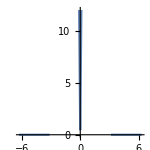

```mathematica
Plot[f[θ],{θ,-2π,2π},ImageSize->150,AspectRatio->Automatic, PlotRange->{0,12}]
```

Again I see that f(θ) is an even function. Also the problem description tells me to use (20), which is a periodic function. I assume again that the period of f(θ) is 2π. I am advised to use numbered line (6*) from p. 486:

a_0=1/L∫_0^L f[x]ⅆx,    a_n=2/L∫_0^L f[x]Cos[(n π x)/L]ⅆx,   n=1,2,...

and taking L = π, and noting that an even f(θ) implies b_n=0, I can begin calculations:

```mathematica
Subscript[a, 0]=1/π∫_0^π f[x]ⅆx
```

55 π

```mathematica
an=2/π∫_0^π f[x]Cos[(n π x)/π]ⅆx
```

(220 (-1+Cos[n π]+n π Sin[n π]))/(n^2 π)

```mathematica
u[r_,θ_]=Subscript[a, 0]+Sum[an(r)^n Cos[n θ],{n,1,7,2}];
```

```mathematica
u[r,θ]
```

55 π-(440 r Cos[θ])/π-(440 r^3 Cos[3 θ])/(9 π)-(88 r^5 Cos[5 θ])/(5 π)-(440 r^7 Cos[7 θ])/(49 π)

The expression in the green cell above matches the answer in the text.

11. Semidisk. Find the steady-state temperature in a semicircular thin plate r=a kept at constant temperature u_0 and the segment -a<x<a at 0 .

This problem is worked in the s.m., but briefly, and seems to establish that a disk with both faces heated has an average, or possibly zero, temperature in the median plane.

15. Tension. Find a formula for the tension required to produce a desired fundamental frequency f_1 of a drum.

```mathematica
Clear["Global`*"]
```

The variables for tension, T and density, ρ, have entered the calculations before. Assume the starting tension T=12.5 lbs/ft, and the density of the drum covering is 2.5 slugs/ft^2.

The s.m. refers to p. 588 and states that the frequency, in cycles per unit time, equals λ_m/2π. This interesting formula I can’t find in the text. Instead, I located a simple online version from http://hyperphysics.phy-astr.gsu.edu/hbase/Music/cirmem.html, which use a different mass system but seems general.

And in the above formula T=membrane tension in Newtons/meter; σ=density in kg/meter^2 ; D=diameter of membrane in meters. And f is in Hertz. So to do the conversions of the assumptions made above,

f_1==0.766(√(T/σ))/D

If I prescribe f in hertz, then T yields some pretty big numbers for tension. The tempered scale for C_0, D_1, E_4, F_6, and B_8:

```mathematica
tab1=Table[Solve[0.766(√(T/3.389))/0.3==f,{T}],{f,{16.35,36.71,329.63,1396.91,7902.13}}];
```

```mathematica
fl={"frequency",16.35,36.71,329.63,1396.91,7902.13};
```

```mathematica
tab2 =Flatten[{"tension",Flatten[tab1]}];
```

```mathematica
sc={"note","C_0","D_1","E_4","F_6","B_8"};
```

```mathematica
Grid[{sc,fl,tab2},Frame->All]
```

note | C_0 | D_1 | E_4 | F_6 | B_8
frequency | 16.35 | 36.71 | 329.63 | 1396.91 | 7902.13
tension | T→138.961 | T→700.528 | T→56482. | T→1.01436×10^6 | T→3.24597×10^7

25. Semicircular membrane. Show that u_11 represents the fundamental mode of a semicircular membrane and find the corresponding frequency when c^2 = 1 and R = 1.

EXTRA INSERTED MATERIAL

```mathematica
Clear["Global`*"]
```

For an example in the text where f(r) is considered instead of f(θ), see example 1 on p. 590. To go through a complete example from Fasshauer’s wave.nb, (http://math.iit.edu/~fass/461_handouts.html):

We consider the general wave equation on a disk of radius R
	u_tt = c^2 (((r u_r)_r)/r +u_θθ/r^2)
subject to the boundary condition
	u(R,θ,t)=0
and initial conditions
	u(r,θ,0)=f(r,θ),
	u_t(r,θ,0)=g(r,θ).
If the problem is circularly symmetric then the PDE simplifies to
	u_tt = c^2 ((r u_r)_r)/r.
If, in addition, we assume that the initial velocity is zero, then the boundary and initial conditions become
	u(R,t)=0,
	u(r,0)=f(r),
	u_t(r,0)=0.
We set some parameters and define the initial displacement:

```mathematica
c=1;R=2;
f[r_]=(1-r/R)^4 (4 r/R+1);
```

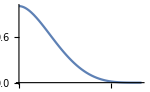

```mathematica
Plot[f[r],{r,0,R},ImageSize->150]
```

```mathematica
RevolutionPlot3D[f[r],{r,0,R},ImageSize->150]
```

-Graphics3D-

We showed that, for general initial position f and general initial velocity g, the solution is of the form
	u(r,t) = ∑_(n=1)^∞ (a_n cos(√λ_n c t)+b_n sin(√λ_n c t))J_0(√λ_n r)
with
	a_n=(∫_0^R f(r)J_0(√λ_n r)rⅆr)/(∫_0^R (J_0(√λ_n r))^2 rⅆr)  and  b_n=(∫_0^R g(r)J_0(√λ_n r)rⅆr)/(∫_0^R (J_0(√λ_n r))^2 rⅆr).
Since we assumed the initial velocity to be zero we have b_n=0.
First, we know that the eigenvalues are given by
	λ_n= (z_n/R)^2,
where z_n is the n-th zero of the Bessel function J_0.

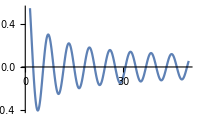

```mathematica
Plot[BesselJ[0,r],{r,0,50},ImageSize->200]
```

The zeros of the Bessel function look almost equally spaced, but they are not. However, their spacing approaches π. Here are the first 16 zeros from the graph above along wih their spacing:

```mathematica
Grid[{{Grid[Table[{i,BesselJZero[0,i]//N,BesselJZero[0,i]//N-0},{i,1}]]},{Grid[Table[{i,BesselJZero[0,i]//N,BesselJZero[0,i]-BesselJZero[0,i-1]//N},{i,2,16}]]}},Alignment->"."]
```

1 | 2.40483 | 2.40483
2 | 5.52008 | 3.11525
3 | 8.65373 | 3.13365
4 | 11.7915 | 3.13781
5 | 14.9309 | 3.13938
6 | 18.0711 | 3.14015
7 | 21.2116 | 3.14057
8 | 24.3525 | 3.14083
9 | 27.4935 | 3.14101
10 | 30.6346 | 3.14113
11 | 33.7758 | 3.14121
12 | 36.9171 | 3.14128
13 | 40.0584 | 3.14133
14 | 43.1998 | 3.14137
15 | 46.3412 | 3.1414
16 | 49.4826 | 3.14142

The eigenvalues are given by

```mathematica
Lambda[n_]=N[(BesselJZero[0,n]/R)^2];
Table[Lambda[n],{n,1,16}]
```

{1.4458,7.61782,18.7218,34.7601,55.7331,81.6408,112.483,148.261,188.973,234.62,285.202,340.718,401.169,466.556,536.876,612.132}

We now compute the Fourier coefficients a_n:

```mathematica
a[n_] = Integrate[f[r]BesselJ[0,Sqrt[Lambda[n]]r] r,{r,0,R}]/Integrate[BesselJ[0,Sqrt[Lambda[n]]r]^2 r,{r,0,R}];
Table[a[n],{n,1,10}]
```

{0.432885,0.407986,0.110033,0.0239338,0.0126202,0.00457419,0.0030777,0.0014233,0.00108219,0.000577441}

In our setting, the N-th partial sum of the Fourier series solution of the wave equation is
	u(r,t) = ∑_(n=1)^N a_n cos(√λ_n c t)J_0(√λ_n r).

```mathematica
u[r_,t_,N_]=Sum[a[n] Cos[Sqrt[Lambda[n]]c t]BesselJ[0,Sqrt[Lambda[n]]r],{n,1,N}];
uplot=u[r,t,20];
```

We plot the (partial sum approximation to the) solution at time t=0.

```mathematica
RevolutionPlot3D[uplot/.t->0,{r,0,R},ImageSize->200]
```

-Graphics3D-

Some more plots at different times t:

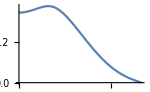

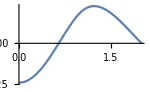

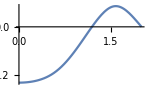

```mathematica
Plot[uplot/.t->0.5,{r,0,R},ImageSize->150]
Plot[uplot/.t->1.0,{r,0,R},ImageSize->150]
Plot[uplot/.t->1.5,{r,0,R},ImageSize->150]
```

```mathematica
Manipulate[RevolutionPlot3D[uplot/.t->tplot,{r,0,R},PlotRange->{All,All,{-1,1}}],{tplot,0,10}]
```

RevolutionPlot3D::plln: Limiting value R in {r,0,R} is not a machine-sized real number.